```mathematica
HC1:=B''[r]+B[r]*(X'[r]-2*A'[r])+B'[r]*(-2*A[r]+X[r]+2*G[r])-2*G[r]*B[r]*(A[r]-X[r]+G[r]);
HC2:=F''[r]+F[r]*(X'[r]-2*G'[r])+F'[r]*(A[r]+X[r]-G[r])+F[r]*(G[r]*(X[r]-A[r]-2G[r])-A[r]*(A[r]-X[r]))-G[r];
```

## First case

```mathematica
eq1:=X[r]+2G[r]-A[r]==Subscript[k, B]^2;
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==Subscript[ω, B]^2;
eq3:=A[r]+X[r]-G[r]==Subscript[k, F]^2;
eq4:=X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r]==Subscript[ω, F]^2;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

A[r]+k_B^2==2 G[r]+X[r]

ω_B^2+2 G[r] (A[r]+G[r]-X[r])+2 A'[r]==X'[r]

A[r]+X[r]==G[r]+k_F^2

A[r]^2+A[r] G[r]+2 G[r]^2+ω_F^2+2 G'[r]==(A[r]+G[r]) X[r]+X'[r]

```mathematica
FullSimplify[Solve[eq1,A[r]]]
```

{{A[r]→2 G[r]-k_B^2+X[r]}}

```mathematica
A[r_]:=2 G[r]-Subscript[k, B]^2+X[r];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

6 G[r]^2+ω_B^2+4 G'[r]+X'[r]==2 G[r] k_B^2

G[r]+2 X[r]==k_B^2+k_F^2

k_B^4+ω_F^2+2 G[r] (4 G[r]+X[r])+2 G'[r]==k_B^2 (5 G[r]+X[r])+X'[r]

```mathematica
FullSimplify[Solve[eq3,X[r]]]
```

{{X[r]→1/2 (-G[r]+k_B^2+k_F^2)}}

```mathematica
X[r_]:=1/2 (-G[r]+Subscript[k, B]^2+Subscript[k, F]^2);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

2 G[r] k_B^2==6 G[r]^2+ω_B^2+(7 G'[r])/2

True

14 G[r]^2+k_B^4+(2 G[r]-k_B^2) k_F^2+2 ω_F^2+5 G'[r]==7 G[r] k_B^2

```mathematica
FullSimplify[DSolve[eq2,G[r],r]]
FullSimplify[DSolve[eq4,G[r],r]]
```

{{G[r]→1/6 (k_B^2-√(-k_B^4+6 ω_B^2) Tan[1/7 (2 r-7 C[1]) √(-k_B^4+6 ω_B^2)])}}

{{G[r]→1/28 (7 k_B^2-2 k_F^2-√(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2) Tan[1/10 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)])}}

```mathematica
G[r_]:=1/28 (7 Subscript[k, B]^2-2 Subscript[k, F]^2-√(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2) Tan[1/10 (r-5 C[1]) √(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2)]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

1/3920 Sec[1/10 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)]^2 (70 Sin[1/5 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)] k_B^2 √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)-60 Sin[1/5 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)] k_F^2 √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)+10 Cos[1/5 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)] (35 k_B^4-28 k_B^2 k_F^2-12 k_F^4+168 ω_F^2)+7 (69 k_B^4-116 k_B^2 k_F^2-28 k_F^4+544 ω_F^2))==ω_B^2

True

True

```mathematica
FullSimplify[1/28 (7 Subscript[k, B]^2-2 Subscript[k, F]^2-√(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2) Tan[1/10 (r-5 C[1]) √(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2)])==1/6 (Subscript[k, B]^2-√(-Subscript[k, B]^4+6 Subscript[ω, B]^2) Tan[1/7 (2 r-7 C[1]) √(-Subscript[k, B]^4+6 Subscript[ω, B]^2)])]
```

7 (k_B^2+2 √(-k_B^4+6 ω_B^2) Tan[1/7 (2 r-7 C[1]) √(-k_B^4+6 ω_B^2)])==6 k_F^2+3 √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2) Tan[1/10 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)]

## Second case

```mathematica
eq1:=X[r]+2G[r]-A[r]==0;
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==0;
eq3:=A[r]+X[r]-G[r]==0;
eq4:=X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r]==0;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

A[r]==2 G[r]+X[r]

2 (G[r] (A[r]+G[r]-X[r])+A'[r])==X'[r]

A[r]+X[r]==G[r]

(A[r]+G[r]) X[r]+X'[r]==A[r]^2+A[r] G[r]+2 (G[r]^2+G'[r])

```mathematica
FullSimplify[Solve[eq1,A[r]]]
```

{{A[r]→2 G[r]+X[r]}}

```mathematica
A[r_]:=2 G[r]+X[r];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

6 G[r]^2+4 G'[r]+X'[r]==0

G[r]+2 X[r]==0

X'[r]==2 (G[r] (4 G[r]+X[r])+G'[r])

```mathematica
FullSimplify[Solve[eq3,X[r]]]
```

{{X[r]→-G[r]/2}}

```mathematica
X[r_]:=1/2 (-G[r]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

12 G[r]^2+7 G'[r]==0

True

14 G[r]^2+5 G'[r]==0

```mathematica
FullSimplify[DSolve[eq2,G[r],r]]
FullSimplify[DSolve[eq4,G[r],r]]
```

{{G[r]→7/(12 r-7 C[1])}}

{{G[r]→5/(14 r-5 C[1])}}

```mathematica
G[r_]:=7/(12 r-7 C[1]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

True

True

1/(12 r-7 C[1])==0

```mathematica
FullSimplify[1/28 (7 Subscript[k, B]^2-2 Subscript[k, F]^2-√(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2) Tan[1/10 (r-5 C[1]) √(7 Subscript[k, B]^4-28 Subscript[k, B]^2 Subscript[k, F]^2-4 Subscript[k, F]^4+112 Subscript[ω, F]^2)])==1/6 (Subscript[k, B]^2-√(-Subscript[k, B]^4+6 Subscript[ω, B]^2) Tan[1/7 (2 r-7 C[1]) √(-Subscript[k, B]^4+6 Subscript[ω, B]^2)])]
```

7 (k_B^2+2 √(-k_B^4+6 ω_B^2) Tan[1/7 (2 r-7 C[1]) √(-k_B^4+6 ω_B^2)])==6 k_F^2+3 √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2) Tan[1/10 (r-5 C[1]) √(7 k_B^4-28 k_B^2 k_F^2-4 k_F^4+112 ω_F^2)]

## Forcing the frequencies

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[γ, 1];
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r];
eq3:=A[r]+X[r]-G[r]==Subscript[γ, 2];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

2 A[r]+γ_1==2 G[r]+X[r]

(A[r]-G[r]) (A[r]-X[r])+2 G'[r]==2 A'[r]

A[r]+X[r]==G[r]+γ_2

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+γ_1}}

```mathematica
X[r_]:=2A[r]-2 G[r]+Subscript[γ, 1];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(A[r]-G[r]) (A[r]-2 G[r]+γ_1)+2 (A'[r]-G'[r])==0

3 A[r]+γ_1==3 G[r]+γ_2

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]-γ_1+γ_2)}}

```mathematica
A[r_]:=1/3 (3 G[r]-Subscript[γ, 1]+Subscript[γ, 2]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(3 G[r]-2 γ_1-γ_2) (γ_1-γ_2)==0

True

```mathematica
FullSimplify[DSolve[eq2,G[r],r]]
```

{{G[r]→1/3 (2 γ_1+γ_2)}}

```mathematica
G[r_]:=1/3 (2 Subscript[γ, 1]+Subscript[γ, 2]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

```mathematica
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

1/3 (γ_1+2 γ_2)

1/3 (2 γ_1+γ_2)

1/3 (γ_1+2 γ_2)

```mathematica
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

2 B[r] (2 γ_1+γ_2)^2==9 (γ_1 B'[r]+B''[r])

{{B[r]→ⅇ^(-1/6 r (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2])}}

(2 γ_1+γ_2) (3+2 F[r] (2 γ_1+γ_2))==9 (γ_2 F'[r]+F''[r])

{{F[r]→ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[1]+ⅇ^(1/3 r √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[2])-3/(4 γ_1+2 γ_2)}}

```mathematica
B[r_]:=ⅇ^(-1/6 r (3 Subscript[γ, 1]+√(41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2))) (C[1]+ⅇ^(1/3 r √(41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2)) C[2]);
F[r_]:=ⅇ^(-1/6 r (3 Subscript[γ, 2]+√(32 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+17 Subscript[γ, 2]^2))) (C[3]+ⅇ^(1/3 r √(32 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+17 Subscript[γ, 2]^2)) C[4])-3/(4 Subscript[γ, 1]+2 Subscript[γ, 2]);
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 r (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1] (5 γ_1+4 γ_2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] (5 γ_1+4 γ_2)-C[1] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))

2/9 (γ_1-γ_2) (2 γ_1+γ_2)

1/6 (-6+(18 γ_1)/(2 γ_1+γ_2)+ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4]) (4 γ_1+5 γ_2)-ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[3] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)+ⅇ^(1/6 r (-3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[4] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+1/2 (2 ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(2 γ_1+γ_2)) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)+r''[τ]

2/3 (2 γ_1+γ_2) r'[τ] θ'[τ]-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

2/3 (2 γ_1+γ_2) r'[τ] ϕ'[τ]+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+(ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2)) ϕ'[τ]^2+r''[τ]

2/3 (2 γ_1+γ_2) r'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
DSolve[2/3 (2 Subscript[γ, 1]+Subscript[γ, 2]) r'[τ] ϕ'[τ]+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+ⅇ^(-4/3 r[K[1]] γ_1-2/3 r[K[1]] γ_2) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-4/3 r[K[1]] Subscript[γ, 1]-2/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ,τ]
```

ⅇ^(-4/3 r[τ] γ_1-2/3 r[τ] γ_2) C[1]

```mathematica
ϕ[τ_]:=C[2]+ⅇ^(-4/3 r[K[1]] Subscript[γ, 1]-2/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

ⅇ^(-4/3 r[τ] (2 γ_1+γ_2)) C[1]^2 (ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2))+1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[2/3 (Subscript[γ, 1]+2 Subscript[γ, 2]) r'[τ] t'[τ]+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+ⅇ^(-2/3 r[K[1]] γ_1-4/3 r[K[1]] γ_2) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-2/3 r[K[1]] Subscript[γ, 1]-4/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ,τ]
```

ⅇ^(-2/3 r[τ] γ_1-4/3 r[τ] γ_2) C[1]

```mathematica
t[τ_]:=C[2]+ⅇ^(-2/3 r[K[1]] Subscript[γ, 1]-4/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

ⅇ^(-1/6 r[τ] (11 γ_1+16 γ_2+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) C[1]^2 (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2])+ⅇ^(-4/3 r[τ] (2 γ_1+γ_2)) C[1]^2 (ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2))+1/3 (γ_1+2 γ_2) r'[τ]^2+r''[τ]

0

```mathematica
Subscript[γ, 1]=1;Subscript[γ, 2]=-3;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}]
```

3/2 ⅇ^((4 r[τ])/3)+2 ⅇ^((37 r[τ])/6) Cosh[1/6 √17 r[τ]]+2 ⅇ^((17 r[τ])/6) Cosh[1/6 √89 r[τ]]-5/3 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

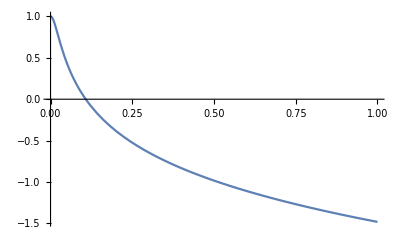

```mathematica
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,0,1}]
Plot[r[τ]/.s,{τ,0,1}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√17) r) (-((7+√17) C[1])+(-7+√17) ⅇ^((√17 r)/3) C[2])

-8/9

-4+1/6 ⅇ^(-1/6 (-9+√89) r) (-((11+√89) C[3])+(-11+√89) ⅇ^((√89 r)/3) C[4])